## HW 8 - 5.1, 5.2, 5.17

### #5 .2

```mathematica
u = (x-1)*(y-0.5)*(a1 + a2*x + a3*y)
```

(-1+x) (-0.5+y) (a1+a2 x+a3 y)

```mathematica
ux = D[u,x]
```

a2 (-1+x) (-0.5+y)+(-0.5+y) (a1+a2 x+a3 y)

```mathematica
uy = D[u,y]
```

a3 (-1+x) (-0.5+y)+(-1+x) (a1+a2 x+a3 y)

```mathematica
N1 = D[u,a1]
```

(-1+x) (-0.5+y)

```mathematica
N2 = D[u,a2]
```

(-1+x) x (-0.5+y)

```mathematica
N3 = D[u,a3]
```

(-1+x) (-0.5+y) y

```mathematica
N1x = D[N1, x]
```

-0.5+y

```mathematica
N1y = D[N1,y]
```

-1+x

```mathematica
N2x=D[N2,x]
```

(-1+x) (-0.5+y)+x (-0.5+y)

```mathematica
N2y = D[N2,y]
```

(-1+x) x

```mathematica
N3x = D[N3,x]
```

(-0.5+y) y

```mathematica
N3y = D[N3, y]
```

(-1+x) (-0.5+y)+(-1+x) y

```mathematica
WF[Ni_] := Integrate[ux * D[Ni, x] + uy*D[Ni,y] + Ni , {x, 0,1},{y,0,0.5}]
```

```mathematica
G1 = WF[N1]
```

0.0625+0.208333 a1+0.0416667 a2+0.00520833 a3

```mathematica
G2 =WF[N2]
```

0.0208333+0.0416667 a1+0.0305556 a2

```mathematica
G3 = WF[N3]
```

0.0104167+0.00520833 a1+0.0149306 a3

```mathematica
{{G1}, {G2},{G3}} == {{0},{0},{0}}
```

{{0.0625+0.208333 a1+0.0416667 a2+0.00520833 a3},{0.0208333+0.0416667 a1+0.0305556 a2},{0.0104167+0.00520833 a1+0.0149306 a3}}=={{0},{0},{0}}

```mathematica
Solve[%20,{a1,a2,a3}]
```

{{a1→-0.203457,a2→-0.404377,a3→-0.626701}}

### #5 .17

#### a) Governing Equation and Boundary Conditions for Torsion

```mathematica
Clear[ϕ]
```

```mathematica
Tors[ϕ_] := D[ϕ,{x,2}] + D[ϕ,{y,2}] + 2*G*θ;
```

```mathematica
ϕ[x_,y_,h_] := -G*(-2*h^2/27 + 1/2*(x^2+y^2) - (x^3 - 3*x*y^2)/(2*h))*θ
```

```mathematica
Tors[ϕ[x,y,h]]
```

2 G θ-G (1-(3 x)/h) θ-G (1+(3 x)/h) θ

```mathematica
Simplify[2 G θ-G (1-(3 x)/h) θ-G (1+(3 x)/h) θ]
```

0

```mathematica
ϕ[10/3,0,5]
```

0

#### b) Exact Solution

#### Torsional Constant, J

```mathematica
a= Triangle[{{10/3,0},{-5/3, 5/Sqrt[3]},{-5/3,-5/Sqrt[3]}}]
```

Triangle[{{10/3,0},{-5/3,5/(√3)},{-5/3,-5/(√3)}}]

```mathematica
J = N[Integrate[ϕ[x,y,5], {x,y} ∈ a] /. G*θ -> 1]
```

12.0281

```mathematica
Graphics[a]
```

-Graphics-

```mathematica
G = 70/(2*(1+0.33))
```

26.3158

#### Angle of Twist per Unit Length, θ

```mathematica
θ = 500/J*10^-8/G*10^9
```

15.7963

#### Maximum Shear Stress, τ

```mathematica
τx = D[ϕ[x,y,5],x]
```

-415.692 (x+1/10 (-3 x^2+3 y^2))

```mathematica
τy = D[ϕ[x,y,5],y]
```

-415.692 (y+(3 x y)/5)

```mathematica
τmax = Sqrt[τx^2 + τy^2]/. {x-> 5/6, y -> 5/(2*Sqrt[3])}
```

1039.23

```mathematica
τ = G*θ*5/2
```

1039.23

#### c) Finite Element Analysis using Triangular Elements

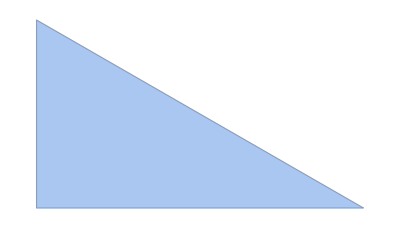

```mathematica
b =BoundaryMeshRegion[{{10/3,0},{-5/3, 5/Sqrt[3]},{-5/3,0}}, Line[{1,2,3,1}]]
```

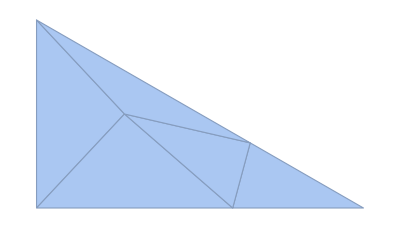

```mathematica
t =TriangulateMesh[b, MaxCellMeasure->2.3]
```

```mathematica
data =Flatten[MeshPrimitives[t,2]]//TableForm
```

Polygon[{{-1.66667,0.},{-0.321367,1.44338},{-1.66667,2.88675}}]
Polygon[{{1.33333,0.},{-0.321367,1.44338},{-1.66667,0.}}]
Polygon[{{1.33333,0.},{3.33333,0.},{1.60128,1.}}]
Polygon[{{-0.321367,1.44338},{1.33333,0.},{1.60128,1.}}]
Polygon[{{1.60128,1.},{-1.66667,2.88675},{-0.321367,1.44338}}]

```mathematica
vertices = MeshCoordinates[t]
```

{{3.33333,0.},{-1.66667,2.88675},{-1.66667,0.},{1.60128,1.},{1.33333,0.},{-0.321367,1.44338}}

```mathematica
l =Table[{i , vertices[[i]]},{i,1,Length[vertices]}]//TableForm
```

1 | 3.33333
0.
2 | -1.66667
2.88675
3 | -1.66667
0.
4 | 1.60128
1.
5 | 1.33333
0.
6 | -0.321367
1.44338

```mathematica
TriElement[x1_,x2_,x3_,y1_,y2_,y3_] := Module[{A,N1,N2,N3,n,B,c},A= (1/2*(-x2*y1+ x3*y1+ x1*y2-x3*y2-x1*y3+x2*y3));N1= 1/2/A *(x3*(y-y2)+x*(y2-y3)+x2*(-y+y3));N2= 1/2/A *(x3*(-y-y1)+x1*(y-y3)+x*(-y1+y3));N3= 1/2A *(x2(y-y1)+x*(y1-y2)+x1*(-y+y2));n={{N1},{N2},{N3}};B={{D[N1,x] ,D[N1,y]},{D[N2,x],D[N2,y]},{D[N3,x] ,D[N3,y]}};
c= {{1,0},{0,1}}; A*B.c.Bᵀ  ]
```

```mathematica
r[x1_,x2_,x3_,y1_,y2_,y3_] := Module[{A,N1,N2,N3,n,B,c},A= (1/2*(-x2*y1+ x3*y1+ x1*y2-x3*y2-x1*y3+x2*y3));N1= 1/2/A *(x3*(y-y2)+x*(y2-y3)+x2*(-y+y3));N2= 1/2/A *(x3*(-y-y1)+x1*(y-y3)+x*(-y1+y3));N3= 1/2A *(x2(y-y1)+x*(y1-y2)+x1*(-y+y2));n={{1},{1},{1}}; n*2*A/3]
```

```mathematica
r = Table[r[data[[1,i,1,1,1]],data[[1,i,1,1,2]],data[[1,i,1,2,1]],data[[1,i,1,2,2]],data[[1,i,1,3,1]],data[[1,i,1,3,2]]],{i,1,Length[data[[1]]]}] //TableForm
```

2.19652 | 2.19652 | 2.19652
-1.0739 | -1.0739 | -1.0739
-1.51197 | -1.51197 | -1.51197
-0.294967 | -0.294967 | -0.294967
-3.20536 | -3.20536 | -3.20536

```mathematica
kel = Table[{data[[1,i]] ,TriElement[data[[1,i,1,1,1]],data[[1,i,1,1,2]],data[[1,i,1,2,1]],data[[1,i,1,2,2]],data[[1,i,1,3,1]],data[[1,i,1,3,2]]]},{i,1,Length[data[[1]]]}] //TableForm
```

Polygon[{{-1.66667,0.},{-0.321367,1.44338},{-1.66667,2.88675}}] | 1.58105 | -0.465885 | -12.1058
-0.465885 | 0.295404 | 1.85067
-12.1058 | 1.85067 | 111.325
Polygon[{{1.33333,0.},{-0.321367,1.44338},{-1.66667,0.}}] | -0.447134 | -0.29082 | 1.91486
-0.29082 | -0.748267 | 2.69624
1.91486 | 2.69624 | -11.965
Polygon[{{1.33333,0.},{3.33333,0.},{1.60128,1.}}] | -1.26465 | 0.668598 | 3.06585
0.668598 | -0.551159 | -0.604059
3.06585 | -0.604059 | -12.6625
Polygon[{{-0.321367,1.44338},{1.33333,0.},{1.60128,1.}}] | -0.211126 | -0.442632 | 0.127981
-0.442632 | -2.11212 | 0.500124
0.127981 | 0.500124 | -0.122959
Polygon[{{1.60128,1.},{-1.66667,2.88675},{-0.321367,1.44338}}] | -0.531683 | 0.320678 | 4.87786
0.320678 | -0.663618 | 7.92784
4.87786 | 7.92784 | -296.033

```mathematica
pts = {{3,6,2},{5,6,2},{5,1,4},{6,5,4},{4,2,6}}
```

{{3,6,2},{5,6,2},{5,1,4},{6,5,4},{4,2,6}}

```mathematica
Length[pts]
```

5

```mathematica
kel[[1,2,2]]
```

{{-0.447134,-0.29082,1.91486},{-0.29082,-0.748267,2.69624},{1.91486,2.69624,-11.965}}

```mathematica
k0 = ConstantArray[0,{Length[l[[1]]],Length[l[[1]]]}];
```

```mathematica
Do[k0[[pts[[i]],pts[[i]]]] += kel[[1,i,2]],{i,1Length[pts]}]
```

```mathematica
k0//MatrixForm
```

(-0.551159 | 0 | 0 | -0.604059 | 0.668598 | 0
0 | 98.6969 | -12.1058 | 0.320678 | 1.91486 | 12.4748
0 | -12.1058 | 1.58105 | 0 | 0 | -0.465885
-0.604059 | 0.320678 | 0 | -13.3171 | 3.56598 | 5.00584
0.668598 | 1.91486 | 0 | 3.56598 | -3.82391 | -0.733451
0 | 12.4748 | -0.465885 | 5.00584 | -0.733451 | -296.697)

```mathematica
r0 = ConstantArray[0,{Length[l[[1]]],1}];
```

```mathematica
Do[r0[[pts[[i]]]] += r[[1,i]],{i,1,Length[pts]}]
```

```mathematica
r0 //MatrixForm
```

(-1.51197
-2.08274
2.19652
-5.0123
-2.88083
-2.37771)

```mathematica
d=ArrayReshape[Flatten[Table[{Symbol["ϕ"<>ToString[j]]},{j,1,Length[pts]}]],{Length[pts],1}];
```

```mathematica
k0.d == r0
```

{{-0.551159,0,0,-0.604059,0.668598,0},{0,98.6969,-12.1058,0.320678,1.91486,12.4748},{0,-12.1058,1.58105,0,0,-0.465885},{-0.604059,0.320678,0,-13.3171,3.56598,5.00584},{0.668598,1.91486,0,3.56598,-3.82391,-0.733451},{0,12.4748,-0.465885,5.00584,-0.733451,-296.697}}.{{ϕ1},{ϕ2},{ϕ3},{ϕ4},{ϕ5}}=={{-1.51197},{-2.08274},{2.19652},{-5.0123},{-2.88083},{-2.37771}}

```mathematica
ϕ1 = ϕ2 = ϕ3 = ϕ4=0
```

0

```mathematica
k0.d ==   r0
```

{{-0.551159,0,0,-0.604059,0.668598,0},{0,98.6969,-12.1058,0.320678,1.91486,12.4748},{0,-12.1058,1.58105,0,0,-0.465885},{-0.604059,0.320678,0,-13.3171,3.56598,5.00584},{0.668598,1.91486,0,3.56598,-3.82391,-0.733451},{0,12.4748,-0.465885,5.00584,-0.733451,-296.697}}.{{0},{0},{0},{0},{ϕ5}}=={{-1.51197},{-2.08274},{2.19652},{-5.0123},{-2.88083},{-2.37771}}

```mathematica
Clear[y]
```

```mathematica
u ={r0[[5]],r0[[6]]}
```

{{-2.88083},{-2.37771}}

```mathematica
g =k0[[5;;6,5;;6]]
```

{{-3.82391,-0.733451},{-0.733451,-296.697}}

```mathematica
{{ϕ5},{ϕ6}}=LinearSolve[g,u]
```

{{0.752193},{0.00615445}}

```mathematica
int[x1_,x2_,x3_,y1_,y2_,y3_] := Module[{A,N1,N2,N3,n,B,c},A= (1/2*(-x2*y1+ x3*y1+ x1*y2-x3*y2-x1*y3+x2*y3));N1= 1/(2*A) *(x3*(y-y2)+x*(y2-y3)+x2*(-y+y3));N2= 1/2/A *(x3*(-y-y1)+x1*(y-y3)+x*(-y1+y3));N3= 1/2A *(x2(y-y1)+x*(y1-y2)+x1*(-y+y2));n={N1,N2,N3}; n]
```

```mathematica
ar[x1_,x2_,x3_,y1_,y2_,y3_] := Module[{A,N1,N2,N3,n,B,c},A= (1/2*(-x2*y1+ x3*y1+ x1*y2-x3*y2-x1*y3+x2*y3));N1= 1/(2*A) *(x3*(y-y2)+x*(y2-y3)+x2*(-y+y3));N2= 1/2/A *(x3*(-y-y1)+x1*(y-y3)+x*(-y1+y3));N3= 1/2A *(x2(y-y1)+x*(y1-y2)+x1*(-y+y2));n={N1,N2,N3}; A]
```

```mathematica
in = Table[int[data[[1,i,1,1,1]],data[[1,i,1,1,2]],data[[1,i,1,2,1]],data[[1,i,1,2,2]],data[[1,i,1,3,1]],data[[1,i,1,3,2]]],{i,1,Length[data[[1]]]}] //TableForm
```

```mathematica
Ar = Abs[Table[ar[data[[1,i,1,1,1]],data[[1,i,1,1,2]],data[[1,i,1,2,1]],data[[1,i,1,2,2]],data[[1,i,1,3,1]],data[[1,i,1,3,2]]],{i,1,Length[data[[1]]]}]] //TableForm
```

3.29478
1.61084
2.26795
0.44245
4.80805

```mathematica
d = {{0},{ϕ5},{ϕ6}}
```

{{0},{0.752193},{0.00615445}}

```mathematica
in[[1,2]]
```

{-0.310396 (0.-1.66667 x-0.321367 (1.66667+y)),-0.310396 (-1.44338 x-0.321367 (-1.44338-y)+1.33333 (0.+y)),-0.805422 (0.+3.11004 x+1.33333 (-1.66667-y))}

```mathematica
ϕxy =Table[in[[1,i]].d,{i,1,Length[data[[1]]]}]// TableForm
```

0.+0.0101388 (0.+3.11004 x-1.66667 (-1.66667-y))+0.114149 (1.44338 x-0.321367 (-1.44338-y)-1.66667 (-2.88675+y))
0.-0.00495693 (0.+3.11004 x+1.33333 (-1.66667-y))-0.233478 (-1.44338 x-0.321367 (-1.44338-y)+1.33333 (0.+y))
0.-0.00697899 (0.-1.60128 x+1.33333 (1.60128-y))-0.165831 (1. x+3.33333 (0.-y)+1.33333 (-1.+y))
0.-0.850031 (1. x+1.33333 (0.-y)-0.321367 (-1.+y))-0.00136152 (-1.60128 x-0.321367 (1.60128-y)+1.44338 (0.+y))
0.-0.0147954 (3.20812 x+1.60128 (-0.321367-y)+1. (-2.88675+y))-0.0782223 (-1.44338 x-1.66667 (-2.88675-y)+1.60128 (-1.44338+y))

```mathematica
ϕx =Table[D[in[[1,i]].d,x],{i,1,Length[data[[1]]]}]// TableForm
```

0.196292
0.32158
-0.154656
-0.847851
0.0654387

```mathematica
ϕy =Table[D[in[[1,i]].d,y],{i,1,Length[data[[1]]]}]// TableForm
```

-0.136667
-0.379727
0.340967
1.40414
-0.24673

```mathematica
Ar[[1,2]]
```

1.61084

```mathematica
ssϕ = Table[(1/3)*Ar[[1,i]]*Total[Flatten[in[[1,i]].d /. {x -> l[[1,pts[[i]],2,1]],y -> l[[1,pts[[i]],2,2]]}]],{i,1,Length[data[[1]]]}]// TableForm
```

0.638927
-1.15264
-0.00739647
0.0586677
-2.84653

```mathematica
J = Abs[4*Total[Total[Flatten[ssϕ]]]]
```

13.2359

```mathematica
τfmax = Max[Table[Sqrt[ϕx[[1,i]]^2 + ϕy[[1,i]]^2],{i,1,Length[ϕx[[1]]]}]]
```

1.64027

```mathematica
G
```

26.3158

```mathematica
θf = 500/J*10^-8/G*10^9
```

14.3549